```mathematica
(*Task0*)
Q={-1,1,2};
R={-4,2,2};
S={-2,1,5};
```

```mathematica
QR=R-Q;
QS=S-Q;
```

```mathematica
normal=Cross[QR,QS]
```

{3,9,1}

```mathematica
randomPoint={x,y,z};
randomVector=randomPoint-Q
```

{1+x,-1+y,-2+z}

```mathematica
randomVector.normal//Simplify
```

-8+3 x+9 y+z

```mathematica
Plot3D[-3 x-9 y+8,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Show[Plot3D[-3 x-9 y+8,{x,-5,5},{y,-5,5}],
ListPointPlot3D[{Q,R,S}]
]
```

-Graphics3D-

```mathematica
Show[Plot3D[-3 x-9 y+8,{x,-5,5},{y,-5,5}],
ListPointPlot3D[{Q,R,S}],
Graphics3D[{Thick,Arrowheads->0.001,Arrow[{Q,R}],
Red,Arrow[{Q,S}],
Arrow[{Q,Q+normal}]}],
BoxRatios->Automatic
]
```

-Graphics3D-

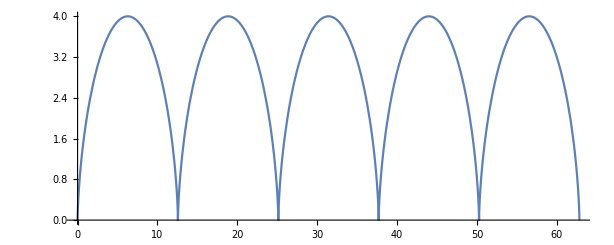

```mathematica
(*Task1*)
r=2;
ParametricPlot[{r(t-Sin[t]),r(1-Cos[t])},{t,0,10Pi}]
```

```mathematica
Manipulate[
Show[
ParametricPlot[{r(tt-Sin[tt]),r(1-Cos[tt])},{tt,0,t},PlotStyle->Red,PlotRange->{{0,60},{0,4}}],
ListPlot[{{r(t-Sin[t]),r(1-Cos[t])}},PlotStyle->Red],
Graphics[Circle[{r*t,r},r]]
],
{t,0.00001,10Pi}
]
```

```mathematica
ExampleData[{"Geometry3D","StanfordBunny"}]
```

-Graphics3D-

```mathematica
vertexData=ExampleData[{"Geometry3D","StanfordBunny"},"VertexData"]
```

{{-0.0927674,-0.0172311,0.130992},{-0.0921802,-0.0172238,0.132348},{-0.0923144,-0.0182222,0.132364},{-0.0874426,-0.0173412,0.110454},{-0.0889612,-0.0183359,0.111861},{-0.0871678,-0.0183619,0.11039},34823,{-0.0453211,-0.035979,0.0345932},{-0.0459209,-0.0375199,0.0346888},{-0.0466394,-0.0392313,0.0345455},{-0.047238,-0.0407654,0.0346371},{-0.047874,-0.0423594,0.0346487}}
 |  |  |  |

```mathematica
polyData=ExampleData[{"Geometry3D","StanfordBunny"},"PolygonData"]
```

{{1,2,3},{4,5,6},{7,8,9},{7,9,10},{11,12,13},{14,15,16},{17,18,19},{20,21,22},{23,24,25},{26,27,28},{29,30,31},{29,31,32},{33,34,35},{33,36,37},{34,38,39},{40,41,42},{34,39,35},{43,44,45},{40,42,46},{46,47,48},{43,45,49},{50,51,39},{52,48,47},{50,39,38},{53,54,51},{53,51,50},69400,{34824,34826,6041},{34824,6041,3615},{34826,34827,6198},{34826,6198,6041},{34827,34828,6199},{34827,6199,6198},{34828,34829,17623},{34828,17623,6199},{34829,34830,15407},{34829,15407,17623},{34830,34831,15408},{34830,15408,15407},{34831,34832,14235},{34831,14235,15408},{34832,34833,14236},{34832,14236,14235},{34833,34834,27856},{34833,27856,14236},{34834,14150,21593},{34834,21593,27856},{4652,2426,1922},{21594,30811,33969},{22194,30811,21590},{21594,21590,30811},{21589,21590,21594}}
 |  |  |  |

```mathematica
vertexData[{{1,2,3}}]
```

{{-0.0927674,-0.0172311,0.130992},{-0.0921802,-0.0172238,0.132348},{-0.0923144,-0.0182222,0.132364},{-0.0874426,-0.0173412,0.110454},{-0.0889612,-0.0183359,0.111861},{-0.0871678,-0.0183619,0.11039},34823,{-0.0453211,-0.035979,0.0345932},{-0.0459209,-0.0375199,0.0346888},{-0.0466394,-0.0392313,0.0345455},{-0.047238,-0.0407654,0.0346371},{-0.047874,-0.0423594,0.0346487}}[{{1,2,3}}]
 |  |  |  |

```mathematica
Graphics3D[GraphicsComplex[vertexData,Polygon[polyData]]]
```

-Graphics3D-

```mathematica
(*Task3*)
ExampleData[{"Geometry3D","SpaceShuttle"}]
```

-Graphics3D-

```mathematica
vertexData=ExampleData[{"Geometry3D","SpaceShuttle"},"VertexData"];
polyData=ExampleData[{"Geometry3D","SpaceShuttle"},"PolygonData"];
```

```mathematica
Graphics3D[GraphicsComplex[vertexData,Polygon[polyData]],Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
rotationMatrix={{1,0,0},{0,Cos[Pi/6],-Sin[Pi/6]},{0,Sin[Pi/6],Cos[Pi/6]}}
```

{{1,0,0},{0,(√3)/2,-1/2},{0,1/2,(√3)/2}}

```mathematica
rotatedRoll30=Table[rotationMatrix.vertexData[[i]],{i,1,Length[vertexData]}];
```

```mathematica
Graphics3D[GraphicsComplex[rotatedRoll30,Polygon[polyData]],Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-